## Quantity/Unit Convenience

### UnitForm: Postfix friendly UnitConvert

```mathematica
UnitForm[units_][quantity_]:=UnitConvert[quantity,units]
UnitForm::usage="like UnitConvert but for postfix";
```

```mathematica
(* Make it so you can always UnitForm 0 into any units *)
(*UnitConvert[zero_?(#==0&),targetunit_]^:=Quantity[0,targetunit]*)
(*UnitConvert[0.,targetunit_]^:=Quantity[0,targetunit]*)
```

#### Example usage

```mathematica
Quantity[10,"Meters/Second"]//N@*UnitForm["mph"]
```

22.3694 mi/h

### ("unit")_q: Interpret a string as a quantity with subscript q

```mathematica
Subscript[s_String, q]:=Quantity[s]
```

#### Example usage

```mathematica
10 Subscript["mph", q]
```

10 mi/h

### loadQuantities: Load common physical quantities, both into the input of the function and globally

```mathematica
ClearAll@loadQuantities;
quantityAssoc[HoldPattern@symb]:=<|ℏ->Quantity["ReducedPlanckConstant"]|>[symb]
(* Makes loadQuantities idempotent, so loadQuantities[loadQuantities[ℏ]]==loadQuantities[ℏ] *)
loadQuantities[q_Quantity]:=q;
(* Define constants that can be loaded *)
loadQuantities[HoldPattern@ℏ]:=ℏ=Quantity["ReducedPlanckConstant"];
loadQuantities[HoldPattern[h]]:=h=Quantity["PlanckConstant"];
loadQuantities[HoldPattern@c]:=c=Quantity["SpeedOfLight"];
loadQuantities[HoldPattern@Subscript[q, e]]:=Subscript[q, e]=Quantity["ElectronCharge"];
loadQuantities[HoldPattern@Subscript[m, e]]:=Subscript[m, e]=Quantity["ElectronMass"];
loadQuantities[HoldPattern@Subscript[m, p]]:=Subscript[m, p]=Quantity["ProtonMass"];
loadQuantities[HoldPattern@Subscript[m, n]]:=Subscript[m, n]=Quantity["NeutronMass"];
loadQuantities[HoldPattern@Subscript[m, μ]]:=Subscript[m, μ]=Quantity["MuonMass"];
loadQuantities[HoldPattern@Subscript[m, τ]]:=Subscript[m, τ]=Quantity["TauMass"];
loadQuantities[HoldPattern@Subscript[ϵ, 0]]:=Subscript[ϵ, 0]=Quantity["VacuumPermittivity"];
loadQuantities[HoldPattern@Subscript[μ, 0]]:=Subscript[μ, 0]=Quantity["VacuumPermeability"];
loadQuantities[HoldPattern@Subscript[a, 0]]:=Subscript[a, 0]=Quantity["BohrRadius"];
loadQuantities[HoldPattern@G]:=G=Quantity["GravitationalConstant"];
loadQuantities[HoldPattern@Subscript[N, A]]:=Subscript[N, A]=Quantity["AvogadroConstant"];
loadQuantities[HoldPattern@Subscript[k, B]]:=Subscript[k, B]=Quantity["BoltzmannConstant"];
(* Allow list of quantities to be loaded  *)
SetAttributes[loadQuantities,Listable]
(*(* Handle other symbols not defined above, and return 0 *)
loadQuantities::unknownSymb="Unknown symbol `1`";
loadQuantities[symb_]:=(Message[loadQuantities::unknownSymb,symb];symb);*)
(* Return unknown symbols unchanged *)
loadQuantities[symb_]:=symb;
(* Load product, sum, etc of constants at once *)
loadQuantities[HoldPattern[f_[symbs__]]]:=f@@loadQuantities[{symbs}]
(* Allow list of quantities to be loaded without surrounding in brackets *)
loadQuantities[symbs__]:=loadQuantities[{symbs}]
(* With no arguments, load all quantities *)
(* todo figure out how to not have to hardcode the -5 (# of non-definition defs) *)
loadQuantities[]:=(Keys[DownValues[loadQuantities]]/.loadQuantities->List)[[;;-5,1]]//Flatten//ReleaseHold//loadQuantities
```

#### Example usage:

Load some quantities, then use them

```mathematica
loadQuantities[Subscript[μ, 0],Subscript[q, e],ℏ,Subscript[m, e],Subscript[a, 0]]
(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)//UnitForm@"Teslas"
Subscript[μ, 0]=.
Subscript[q, e]=.
ℏ=.
Subscript[m, e]=.
Subscript[a, 0]=.
```

{ μ_0, e, ℏ, m_e, a_0}

12.516824 T

Load needed quantities in an expression, and then re-use them

```mathematica
loadQuantities[(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)]//UnitForm@"Teslas"
Subscript[m, e] loadQuantities[c^2]//UnitForm@"keV"
Subscript[μ, 0]=.
Subscript[q, e]=.
ℏ=.
Subscript[m, e]=.
Subscript[a, 0]=.
c=.
```

12.516824 T

510.99895 keV

Load all quantities, then use them

```mathematica
loadQuantities[]
(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)
```

{ c, G, h, ℏ, a_0, k, m_e, m_n, m_p, m_μ, m_τ, N_A, e, ε_0, μ_0}

1/(4 π) e μ_0 ℏ/(m_e a_0^3)

## Side Effects

Useful when you want to keep the value of some expression, but also do something else with it (print it, save it, etc)

### also: Do something as a side effect

```mathematica
also[f_][x_]:=(f@x;x)
```

#### Example usage:

```mathematica
x={2}
y=RandomInteger[10]//also[AppendTo[x,#]&]
x
```

{2}

8

{2,8}

### alsoPrint: Print some thing as a side effect

```mathematica
alsoPrint[f_:Identity]:=also[Print@*f]
```

#### Example usage:

```mathematica
A=RandomInteger[10,{4,4}]//alsoPrint@MatrixForm;
N@Eigenvalues@A
```

(5 | 4 | 10 | 10
6 | 9 | 10 | 6
4 | 4 | 2 | 3
5 | 7 | 2 | 9)

{23.9211,-4.00935,2.54412+1.76634 ⅈ,2.54412-1.76634 ⅈ}

### save, alsoSave: Save a figure as png or svg (as a side effect)

```mathematica
saveDirectory[]:=Module[
	{dir=FileNameJoin@{NotebookDirectory[],"mathematica_figures"}},
	If[
		!DirectoryQ@dir,
		CreateDirectory[FileNameJoin@{NotebookDirectory[],"mathematica_figures"}],
		dir
	]
]
save[fig_,name_String,format_String:"pdf",dpi_Integer:500]:=Export[FileNameJoin@{saveDirectory[],name<>"."<>format},fig,ImageResolution->dpi]
save[fig_,name_String,formats_List,dpi_Integer:500]:=save[fig,name,#,dpi]&/@formats
alsoSave[name_String,format_String:"pdf",dpi_Integer:500]:=also[save[#,name,format,dpi]&]
alsoSave[name_String,formats_List,dpi_Integer:500]:=also[save[#,name,formats,dpi]&]
```

### alsoCopy:

```mathematica
alsoCopyOpts[opts___]:=also[CopyToClipboard@Rasterize[#,opts]&];
alsoCopy=alsoCopyOpts[]
```

also[CopyToClipboard[Rasterize[#1]]&]

### tableHeaded: TableForm but with headers

```mathematica
tableHeaded[headers_][list_]:=TableForm[list,TableHeadings->headers]
tableHeadedRows[rows_][list_]:=TableForm[list,TableHeadings->{rows,None}]
tableHeadedCols[cols_][list_]:=TableForm[list,TableHeadings->{None,cols}]
```

```mathematica
a=RandomInteger[5,4];
b=RandomInteger[10,6];
{a,b}//tableHeadedRows[{"a","b"}]
```

a | 4 | 0 | 3 | 5 |  | 
b | 1 | 2 | 10 | 0 | 4 | 2

## Colors

### defaultColorData: Quicker access to the default plot colors

```mathematica
defaultColorData[]:=ColorData[97]
defaultColorData[n_Integer]:=defaultColorData[][n]
```

#### Example usage:

When combining separate plots with Show, this makes it easier to use the right two colors

```mathematica
f=x^2;
data=Table[{x,f+RandomReal[0.5]},{x,0,2,0.2}];
```

```mathematica
plot=Plot[
f,{x,0,2}
];
```

By default, both are this blue color (ColorData[97][1])

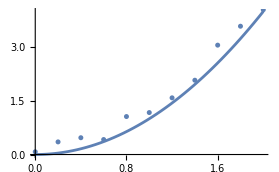

```mathematica
Show[
plot,ListPlot[data]
]
```

To get the same different color as if both were in the same Plot function:

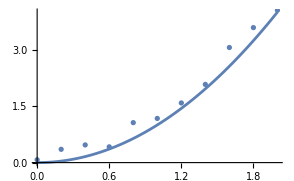

```mathematica
Show[
plot,ListPlot[data,ColorFunction->(defaultColorData[2]&)]
]
```

### Pride Colors!

```mathematica
(* Pride Flags! *)
(* How to add gradients: https://mathematica.stackexchange.com/questions/57885/is-it-possible-to-insert-new-colour-schemes-into-colordata/57893#57893 *)
(* Flag rgb colors: https://www.flagcolorcodes.com/flags/pride *)

ColorData[1];
(* Export this function so users can add gradients as needed *)
insertGradient[name_,gradColors_]:=If[
	!MemberQ[ColorData["Gradients"],name],
	(
		AppendTo[
			DataPaclets`ColorDataDump`colorSchemes,
			{{name,"",{}},{"Gradients"},1,{0,1},gradColors,""}
		];
		AppendTo[
			DataPaclets`ColorDataDump`colorSchemeNames,
			name
		];
	)
]
Module[{data,names,colors},
	data=Import["https://raw.githubusercontent.com/Andrew-Schwartz/YouTilities/master/flags.tsv","TSV","Numeric"->False];
	names=#<>"Flag"&/@data[[;;,1]];
	colors=Map[RGBColor["#"<>#]&,data[[;;,2;;]],{2}];
	
	insertGradient@@#&/@Transpose@{names,colors};
]
```

#### List of Gradients:

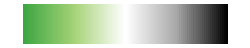
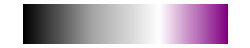
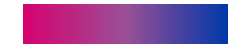
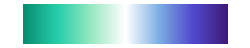
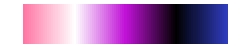
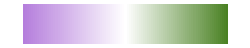
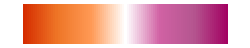
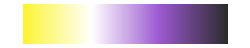
AromanticFlag | -Graphics-
AsexualFlag | -Graphics-
BiFlag | -Graphics-
GayFlag | -Graphics-
GenderfluidFlag | -Graphics-
GenderqueerFlag | -Graphics-
LesbianFlag | -Graphics-
NonbinaryFlag | -Graphics-
NWAromanticFlag | -Graphics-
NWAsexualFlag | -Graphics-
NWGayFlag | -Graphics-
NWGenderfluidFlag | -Graphics-
NWGenderqueerFlag | -Graphics-
NWLesbianFlag | -Graphics-
NWNonbinaryFlag | -Graphics-
NWTransFlag | -Graphics-
OmniFlag | -Graphics-
PanFlag | -Graphics-
PrideFlag | -Graphics-
TransFlag | -Graphics-

```mathematica
With[{data=Select[StringEndsQ@"Flag"]@ColorData@"Gradients"},
TableForm[
ColorData[#,"Image"]&/@data,
TableHeadings->{data,None}
]
]
```

#### Example usage:

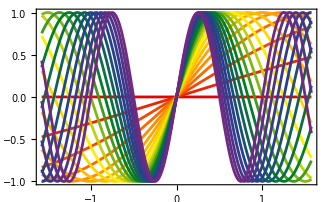

```mathematica
Table[Sin[n π x],{n,0,2,0.1}];
Plot[
%,
{x,-π/2,π/2},
PlotStyle->"PrideFlag"
]
```

## Linear Algebra

### EigvecsT, EigsysT: Wrapper for melt’s functions to allow for getting the eigenvectors as lists of lists, rather than a matrix (row-major vs col-major)

```mathematica
Thread[f[{a,b},{c,d}]]
```

{f[a,c],f[b,d]}

```mathematica
EigvecsT[A_,neigs_:"all",Δ_:10^5]:=Transpose@Eigvecs[A,neigs,Δ]
EigsysT[A_,neigs_:"all",Δ_:10^5]:=MapThread[#1@#2&,{{Identity,Transpose},Eigsys@A}]
```

#### Example Usage:

```mathematica
<<http://www.fmt.if.usp.br/~gtlandi/download/melt.m
(* Eigenvalues of a spin 3/2 Hamiltonian *)
LoadArbitrarySpinMatrices[3/2];
H = Sz + 0.3 Sx.Sx//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
eigenStuff[H]
```

λ | Eigenvector
1.76382 | (0.989021
0.
0.147776
0.)
-1.30398 | (0.
-0.110866
0.
0.993835)
1.05398 | (0.
-0.993835
0.
-0.110866)
-0.0138194 | (0.147776
0.
-0.989021
0.)

```mathematica
EigsysT@H
```

{{-1.30398,-0.0138194,1.05398,1.76382},{{0.,-0.110866,0.,0.993835},{0.147776,0.,-0.989021,0.},{0.,-0.993835,0.,-0.110866},{0.989021,0.,0.147776,0.}}}

```mathematica
eigenStuff[H,sys->EigsysT]
```

λ | Eigenvector
-1.30398 | (0.
-0.110866
0.
0.993835)
-0.0138194 | (0.147776
0.
-0.989021
0.)
1.05398 | (0.
-0.993835
0.
-0.110866)
1.76382 | (0.989021
0.
0.147776
0.)

```mathematica
EigvecsT[H]//tableHeadedCols[{"v_1","v_2","v_3","v_4"}]
```

v_1 | v_2 | v_3 | v_4
0. | -0.110866 | 0. | 0.993835
0.147776 | 0. | -0.989021 | 0.
0. | -0.993835 | 0. | -0.110866
0.989021 | 0. | 0.147776 | 0.

### M_Dot^n: Exponentiate matrices with correct matrix multiplication

Todo: make a more general version that works with kron too I think makes the most sense

```mathematica
(* Exponentiate with something other than Times (useful for matrix powers with Dot) *)
Subscript/:Power[Subscript[mat_,Dot],n_Integer]:=Dot@@Table[mat,n]
```

#### Example usage:

```mathematica
A=PauliMatrix[1]//alsoPrint@MatrixForm;
```

(0 | 1
1 | 0)

The normal exponentiation behavior is to multiply element-wise

```mathematica
Table[MatrixForm[A^n],{n,3}]
```

{(0 | 1
1 | 0),(0 | 1
1 | 0),(0 | 1
1 | 0)}

Using this gets the correct matrix multiplication n times

```mathematica
Table[MatrixForm[Subscript[A, Dot]^n],{n,3}]
```

{(0 | 1
1 | 0),(1 | 0
0 | 1),(0 | 1
1 | 0)}

Another common use case, with melt’s kron function

```mathematica
Subscript/:Power[Subscript[mat_,f_],n_Integer]:=f@@Table[mat,n]/;(Print[DownValues@f];False)
```

```mathematica
kron[mats__]:=KroneckerProduct[mats];
CircleTimes[things__]:=kron[things];
```

```mathematica
Definition[Dot]
```

Attributes[Dot]={Flat,OneIdentity,Protected}

```mathematica
<<https://raw.githubusercontent.com/szhorvat/Spelunking/master/Spelunking.m
```

```mathematica
Spelunk[Dot]
```

Attributes[Dot]={Flat,OneIdentity}

```mathematica
Subscript[A, Dot]^2
```

{{1,0},{0,1}}

```mathematica
Dimensions[Subscript[A, kron]^2]
```

{2}

### eigenStuff: Make a nice lil table of eigenvalues & vectors

matrix: The matrix to calculate the eigenvalues & vectors for
sys: The function used to get the eigens. Must return a tuple of {vals,vecs} Defaults to Eigensystem, but is configurable (mostly for use with melt’s Eigsys for sorting)
aiλ: Whether to show a column for A-Iλ
rref: Whether to show a column for the reduced row echelon form
normalize: Whether to normalize the eigenvectors

```mathematica
ClearAll@eigenStuff
eigenStuff::zeroEigenvectors="Some zero-eigenvectors";
eigenStuff::unequal="#vals!=#vecs";
eigenStuff[matrix_,opts:OptionsPattern[{sys->Eigensystem,aiλ->False,rref->False,normalize->False}]]:=Module[
	{
		aiλ=OptionValue@aiλ,
		rref=OptionValue@rref,
		normalize=OptionValue@normalize,
		sys=OptionValue@sys,
		len=Length@matrix,
		vecs,vals
	},
	{vals,vecs}=sys[matrix];
	vecs=If[normalize,Normalize/@vecs,vecs];
	If[ContainsAny[vecs,{Table[0,len]}],
		Throw[Message[eigenStuff::zeroEigenvectors]]
	];
	AIλ=matrix-# IdentityMatrix@len&/@vals//Simplify;
	If[Length/@{vals,vecs}/.List->Equal,
		Grid[
			Join[
				{{"λ",If[aiλ,"A-Iλ",Nothing],If[rref,"RREF",Nothing],"Eigenvector"}},
				{
					vals,
					If[aiλ,MatrixForm/@AIλ,Nothing],
					If[rref,MatrixForm@*RowReduce/@AIλ,Nothing],
					MatrixForm/@vecs
				}ᵀ
			],
			Frame->All
		],
		Message[eigenStuff::unequal]
	]
]
```

```mathematica
A=RandomInteger[10,{4,4}];
```

```mathematica
eigenStuff[A,rref->False,aiλ->False,normalize->True,sys->Eigsys]//N
```

λ | Eigenvector
-7.04733 | (-0.775882
0.0941402
-0.334806
-0.526355)
-2.64597 | (0.249192
0.36187
0.569483
-0.694725)
4.47617 | (0.328695
-0.729094
0.463801
-0.381144)
19.2171 | (0.509951
0.233938
-0.650125
-0.512407)

### hc (and cc): Add the Hermitian (complex) conjugate of a matrix (value) to itself

```mathematica
CirclePlus[mat_?MatrixQ,hc]:=mat+mat†
CirclePlus[val_,cc]:=val+val*
```

```mathematica
mat={{1, 0, 2}, {0, 1, 0}, {0, 0, 0}};
mat+mat†//MatrixForm
mat⊕hc//MatrixForm
```

(2 | 0 | 2
0 | 2 | 0
2 | 0 | 0)

(2 | 0 | 2
0 | 2 | 0
2 | 0 | 0)

## Miscellaneous

### Enumerate: Like enumerate in every other language

```mathematica
ClearAll[enumerate]
enumerate=MapIndexed[{#2[[1]],#1}&];
```

### SparseReplaceAll: Like ReplaceAll but works with SparseArrays

```mathematica
(* https://mathematica.stackexchange.com/a/154287 *)
SparseReplaceAll[s_SparseArray,rule_]:=With[{
		elems=ReplaceAll[s["NonzeroValues"],rule],
		default=ReplaceAll[s["Background"],rule]
	},
	SparseArray[
		Automatic,
		s["Dimensions"],
		default,
		{1,{s["RowPointers"],s["ColumnIndices"]},elems}
	]
]
```

#### Example Usage

Say we have a sparse matrix with values μ_i above and below the diagonal:

```mathematica
A=SparseArray[
{
Band[{1,2}]->Array[Subscript[μ, #]&,{3}],
Band[{2,1}]->Array[Subscript[μ, #]&,{3}]
},
{4,4}
]
Eigenvalues[A]
```

SparseArray[…]

{-(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),-(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2)}

And we now have specific values of μ_i we want to use:

```mathematica
rules=Array[Subscript[μ, #]->RandomReal[{-10,10}]&,3]
```

{μ_1→-3.44548,μ_2→-6.88547,μ_3→0.45714}

The normal replacement doesn’t work!

```mathematica
A/.rules
ReplaceAll[A,rules] (* equivalent to the above *)
Eigenvalues[%]
```

SparseArray[…]

SparseArray[…]

{-(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),-(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2)}

So we use SparseReplaceAll instead!

```mathematica
SparseReplaceAll[A,rules]
Eigenvalues[%]
```

SparseArray[…]

{-7.71027,7.71027,-0.204282,0.204282}

### fMap: Map a list of functions

```mathematica
ClearAll[fMap]
anyValue_[fMap[innerFunction_]]^:=innerFunction[anyValue]
```

#### Example Usage

```mathematica
m[d_Integer]:=Array[Subscript[a, ##]&,{d,d}]
d[d_]:=m[d]/.Subscript[a, i_,j_]/;i!=j->0
o[d_]:=m[d]/.Subscript[a, i_,j_]/;i==j->0
```

```mathematica
2/@fMap/@{m,d,o};
MatrixForm/@%
```

{(a_(1,1) | a_(1,2)
a_(2,1) | a_(2,2)),(a_(1,1) | 0
0 | a_(2,2)),(0 | a_(1,2)
a_(2,1) | 0)}

### No more laggy/slow chart highlighting!

```mathematica
Charting$InteractiveHighlighting=False;
```

## WIP

### LocalizeAll: Kinda like inverted module?

The idea is to make a scoping function that makes Mathematica behave more like a reasonable language; i.e. rather than having to specify the name of each variable twice (once for the usage and again in the list of local variables), just assume that all variables that appear on the left side of an ‘=’ are local (maybe with a list of exceptions as the first argument?) so each only has to be specified where it is defined.

```mathematica
ClearAll[LocalizeAll];
SetAttributes[LocalizeAll,HoldAll];
LocalizeAll[extra_List,except_List,code_]:=Module[{expressions,locals,f},
expressions=List@@Map[Hold,Hold[code]/.CompoundExpression->List,{2}][[1]];
locals=Join[
Cases[expressions,Hold[Set[lhs_,rhs_]]:>Hold@lhs],
Cases[expressions,Hold[SetDelayed[lhs_[vars___],rhs_]]:>Hold@lhs],
extra
];
f[list_List,exprs_]:=Module[list,CompoundExpression@@(ReleaseHold/@exprs)];
f[Complement[ReleaseHold@locals,except],expressions]
]
```

#### Example

```mathematica
On[Assert]
ClearAll[a]
ClearAll[b]
ClearAll[fn]
hiddenSet[v_Symbol]:=v=ⅇ
returned=LocalizeAll[
{(* any extra variables to localize, incase they were set indirectly *) e},
{(* any variables to exclude from localization, i.e. if you want them to be global *)b},
a=3+1;
hiddenSet[e];
Print[e];
(* This should still be undefined *)
Print["a=",a];
{Mean,Test};
fn[var_]:=var/2;
b=fn[a];
a-b
];
(* Should be true *)
Assert[returned==2]
(* Should be undefined *)
a
DownValues@fn
e
```

{Hold[a],Hold[b],Hold[fn],e}

{a,e,fn}

ⅇ

a=4

a

{}

e

#### Example: if LocalizeAll was implemented using LocalizeAll instead of Module

```mathematica
ClearAll@f
```

```mathematica
localizeAllOuroboros[extra_List,except_List,code_]:=LocalizeAll[{},{},
expressions=List@@Map[Hold,Hold[code]/.CompoundExpression->List,{2}][[1]];
locals=Cases[expressions,Hold[Set[lhs_,rhs_]]:>Hold@lhs];
f[list_List,exprs_]:=Module[list,CompoundExpression@@(ReleaseHold/@exprs)];
f[ReleaseHold@locals,expressions]
]
localizeAllOuroboros[{},{},"heheh"]

(* All of the local variables should be undefined still: *)
expressions
locals
DownValues[f]
```

{Hold[expressions],Hold[locals],Hold[f]}

heheh

expressions

locals

{}